```mathematica
exact = DSolve[{ϵ u'[x] + u[x] == x,u[0]==1},u[x],x]
```

{{u[x]→ⅇ^(-x/ϵ) (1+ⅇ^(x/ϵ) x+ϵ-ⅇ^(x/ϵ) ϵ)}}

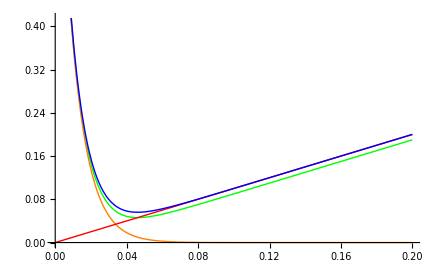

```mathematica
r = ϵ -> .01;
Plot[{(1+ϵ) ⅇ^(-x/ϵ)+(x-ϵ)/. r,ⅇ^(-x/ϵ)/. r,x/. r,ⅇ^(-x/ϵ)+x/. r},{x,0,.2},PlotStyle-> {{Green,Thick},{Orange,Thick},{Red,Thick},{Blue,Thick}}]
```

```mathematica
Manipulate[Plot[{(1+ϵ) ⅇ^(-x/ϵ)+(x-ϵ),ⅇ^(-x/ϵ),x,ⅇ^(-x/ϵ)+x},{x,0,.2},PlotStyle-> {{Green,Thick},{Orange,Thick},{Red,Thick},{Blue,Thick}},PlotRange -> {All,{-0.05,0.5}}] 
,{ϵ,0.0001,0.03}]
```